# Assignment 5 No.5

## (a)

```mathematica
ClearAll["Global`*"]
```

```mathematica
DSolve[x^2*y'[x]+x*(x+2)*y[x]==ⅇ^x,y[x],x]
```

{{y[x]→ⅇ^x/(2 x^2)+(ⅇ^-x C[1])/x^2}}

## (b)

```mathematica
ClearAll["Global`*"]
```

```mathematica
y[x]=ⅇ^x/(2 x^2)+(ⅇ^-x *c1)/x^2
```

(c1 ⅇ^-x)/x^2+ⅇ^x/(2 x^2)

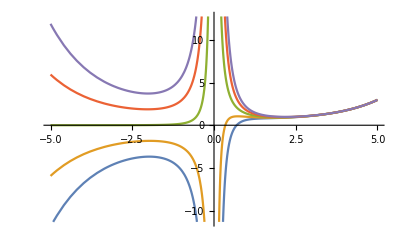

```mathematica
Plot[Evaluate[Table[y[x],{c1,-2,2}]],{x,-5,5}]
```

## (c)

```mathematica
ClearAll["Global`*"]
```

```mathematica
sol1=NDSolve[{y''[x]==y[x]^2,y[0]==0,y'[0]==1},y,{x,1,7}]
```

NDSolve::ndsz: At x == 3.2102, step size is effectively zero; singularity or stiff system suspected.

{{y→InterpolatingFunction[…]}}

```mathematica
Plot[y[x]/.sol1,{x,1,7}]
```

-Graphics-